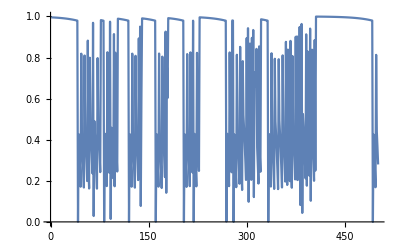

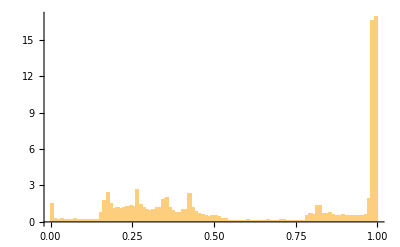

0.02

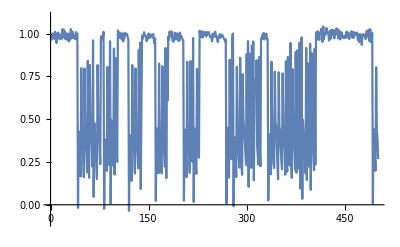

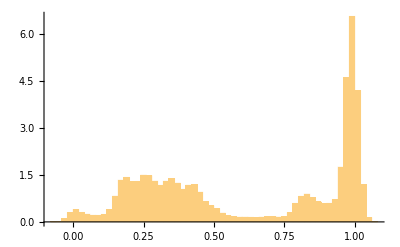

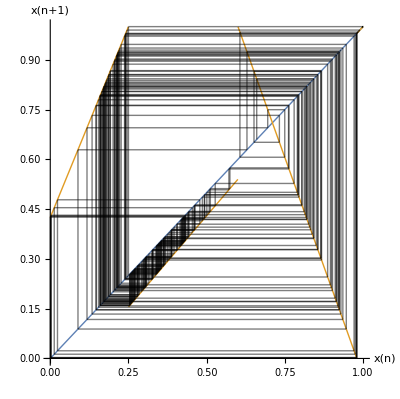

```mathematica
(* three states *)
(* three states *)
a1 =2.3; a2=1.1; a3=1.04;
d1=0.25; d2=0.6;d3=0.98; 
b1=1-d1*a1;
b2=0.9*d2-a2*d2;
f2[x_]:=Piecewise[{ {a1*x+b1,0≤x<d1},{a2*x+b2,d1<x<d2},{(d3-x)/(d3-d2),d2<x<d3},{a3*(x-1)+1, d3<x≤1} }];
steps = 100000;
start = d2*1.1;
orbit=NestList[f2,start,steps];
(* plot time series and histogram *)
ListPlot[Part[orbit, 9100;;9600], Joined->True, PlotRange->{{0,500},{0,1}}]
Histogram[orbit, 100, "PDF"]
(* add white noise *)
std = 0.02
noise =RandomVariate[NormalDistribution[0,std],steps+1];
ListPlot[Part[orbit+noise,9100;;9600], Joined->True, PlotRange->{{0,500},{-0.1,1.1}}]
Histogram[orbit+noise, 50, "PDF"]
(* Cob Web*)
orbit = Part[orbit,1;;300];
lines=Partition[Flatten[{#,#,#,#}&/@orbit][[2;;-2]],2];
Plot[{x,f2[x]},{x,0,1},AspectRatio->Automatic,Epilog->{Opacity[0.5],Line/@Partition[lines,2,1]},PlotStyle->Thick, AxesLabel->{"x(n)","x(n+1)"}, LabelStyle->"Subtitle"]
```

```mathematica
start = d1/2
steps
```

0.125

```mathematica
(* shift switching region *)
```

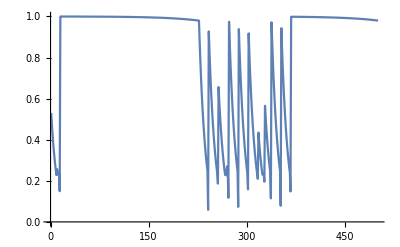

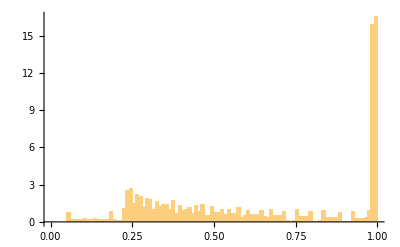

0.02

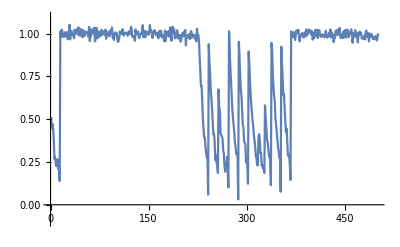

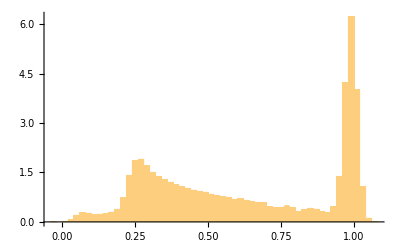

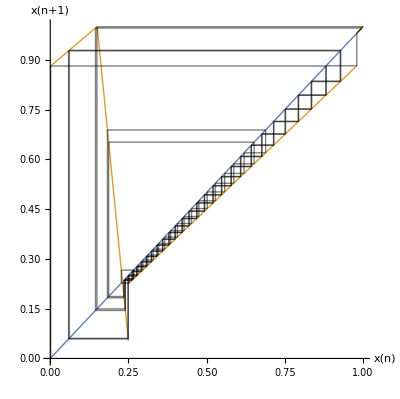

```mathematica
a1 =0.8; a2=0.9; a3=1.02;
d1=0.15; d2=0.25;d3=0.98; 
mswitch = (0.05-1)/(d2-d1); bswitch=1-mswitch*d1;
b1=1-d1*a1;
b2=0.9*d3-a2*d3;
f2[x_]:=Piecewise[{ {a1*x+b1,0≤x<d1},{mswitch*x+bswitch,d1<x<d2},{a2*x+b2,d2<x<d3},{a3*(x-1)+1, d3<x≤1} }];
steps = 100000;
start = d1*0.01;
orbit=NestList[f2,start,steps];
(* plot time series and histogram *)
ListPlot[Part[orbit, 9100;;9600], Joined->True, PlotRange->{{0,500},{0,1}}]
Histogram[orbit, 100, "PDF"]
(* add white noise *)
std = 0.02
noise =RandomVariate[NormalDistribution[0,std],steps+1];
ListPlot[Part[orbit+noise,9100;;9600], Joined->True, PlotRange->{{0,500},{-0.1,1.1}}]
Histogram[orbit+noise, 50, "PDF"]
(* Cob Web*)
orbit = Part[orbit,1;;200];
lines=Partition[Flatten[{#,#,#,#}&/@orbit][[2;;-2]],2];
Plot[{x,f2[x]},{x,0,1},AspectRatio->Automatic,Epilog->{Opacity[0.5],Line/@Partition[lines,2,1]},PlotStyle->Thick, AxesLabel->{"x(n)","x(n+1)"}, LabelStyle->"Subtitle"]
```

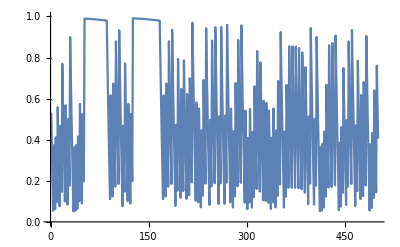

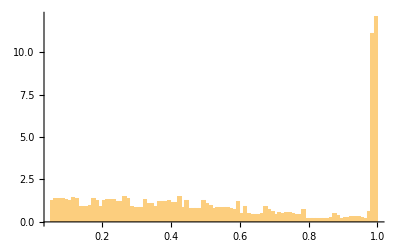

0.02

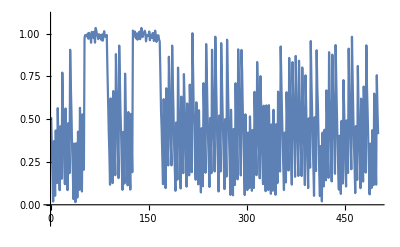

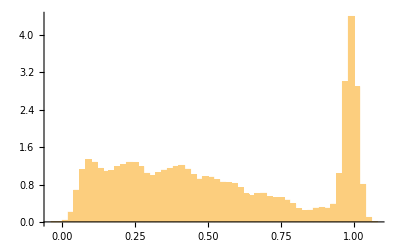

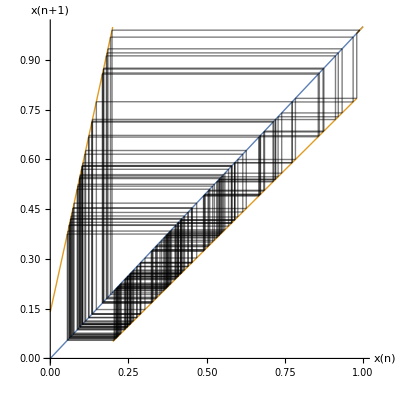

```mathematica
(* no switching region *)
a1 =4.3; a2=.94; a3=1.02;
d1=0.2;d2=0.98; 
b1=1-d1*a1;
b2=0.8*d2-a2*d2;
f2[x_]:=Piecewise[{ {a1*x+b1,0≤x<d1},{a2*x+b2,d1<x<d2},{a3*(x-1)+1, d2<x≤1} }];
steps = 500000;
start = d1*0.5;
orbit=NestList[f2,start,steps];
(* plot time series and histogram *)
ListPlot[Part[orbit, 9100;;9600], Joined->True, PlotRange->{{0,500},{0,1}}]
Histogram[orbit, 100, "PDF"]
(* add white noise *)
std = 0.02
noise =RandomVariate[NormalDistribution[0,std],steps+1];
ListPlot[Part[orbit+noise,9100;;9600], Joined->True, PlotRange->{{0,500},{-0.1,1.1}}]
Histogram[orbit+noise, 50, "PDF"]
(* Cob Web*)
orbit = Part[orbit,1;;200];
lines=Partition[Flatten[{#,#,#,#}&/@orbit][[2;;-2]],2];
Plot[{x,f2[x]},{x,0,1},AspectRatio->Automatic,Epilog->{Opacity[0.5],Line/@Partition[lines,2,1]},PlotStyle->Thick, AxesLabel->{"x(n)","x(n+1)"}, LabelStyle->"Subtitle"]
```